#### Preamble

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

```mathematica
SetDirectory[NotebookDirectory[]]
<<"MaTeX`"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Maxima_Minima.wls"

fs = 9;
texStyle={FontFamily->"Latin Modern Math",FontSize->fs,Black};
graphsOpts= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[ColorData[3,#]]&/@Range[10])};
(*SetOptions[ListLinePlot,graphsOpts];*)
```

/home/juanathan/Documentos/MSc_Thesis/1-Mie

## Redshift of a single particle

```mathematica
dir = "5-Redshift"
plots = ConstantArray[0,{2,2,2}];
radList = Range[5,50,2.];
nMatList = Range[1.,1.8,.04];
(*color-> ext/sca  marcador -> aire/agua -- 12/50,  abierto/cerrado -> correccion*)
markers = {{"●","●",  "○", "○"},{"●","●",  "○", "○"}}(*\[ FilledCircle ]  \[ EmptyCircle ]*);
```


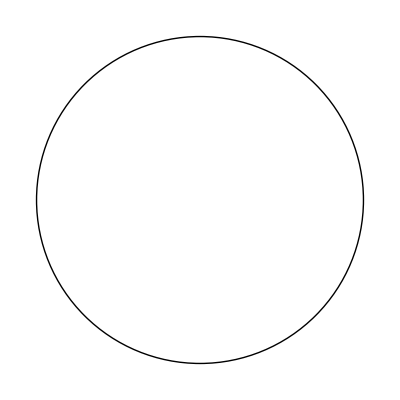

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
markers ={Graphics[{ Disk[{0, 0}]}],Graphics[{ Disk[{0, 0}]}],
Graphics[{Thin,{White,Disk[{0,0}]},Dashing[None], Circle[{0, 0}]}],Graphics[{Thin,Dashing[None], Circle[{0, 0}]}]};
markers  = {markers,markers};
```

#### Radius

```mathematica
ClearAll[radius]
nNP = JohnsonChristyAuRef;

wlength = {490.,700.};
air = glass= plots[[1]];

scaFunc[lda_]:= MieScatteringQ[{nMat[lda],nNP[lda]},lda,radius]
extFunc[lda_]:=  MieExtinctionQ[{nMat[lda],nNP[lda]},lda,radius]
nMat = 1. &;
air[[1]] =Table[radius = rr;
		 FindExtrema[#,wlength, 5., "Maxima"][[1]],
		{rr,radList}]&/@ {extFunc,scaFunc};
nMat = 1.5 &;
glass[[1]] =Table[radius = rr;
		 FindExtrema[#,wlength, 2.5, "Maxima"][[1]],
		{rr,radList}]&/@ {extFunc,scaFunc};
```

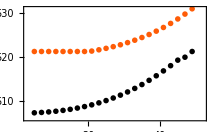
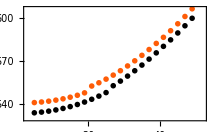

```mathematica
plots[[1,1]] = MapThread[ListPlot[Transpose[{radList,#}]&/@ #[[;;,;;,1]], Mesh->None,PlotMarkers->({#,Scaled[.04]}&/@#2),Evaluate[graphsOpts], PlotRange->{{3,52},{Automatic,Automatic}}]&,{{air[[1]],glass[[1]]},markers}]
```

```mathematica
nNP=JohnsonChristyAuRefSize[#,radius]&;

nMat = 1. &;
air[[2]] =Table[radius = rr;
		 FindExtrema[#,wlength, 5., "Maxima"][[1]],
		{rr,radList}]&/@ {extFunc,scaFunc};
nMat = 1.5&;
glass[[2]] =Table[radius = rr;
		 FindExtrema[#,wlength, 2.5, "Maxima"][[1]],
		{rr,radList}]&/@ {extFunc,scaFunc};
```

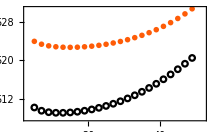
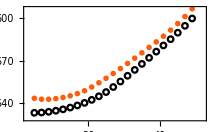

```mathematica
plots[[1,2]] = MapThread[ListPlot[Transpose[{radList,#}]&/@ #[[;;,;;,1]], Mesh->None,PlotMarkers->({#,Scaled[.04]}&/@Reverse@#2),Evaluate[graphsOpts], PlotRange->{{3,52},{Automatic,Automatic}}]&,{{air[[2]],glass[[2]]},markers}]
```

#### Matrix

```mathematica
ClearAll[radius]
nNP = JohnsonChristyAuRef;
wlength = {490.,750.};
r12 = r50= plots[[2]];

scaFunc[lda_]:= MieScatteringQ[{nMat[lda],nNP[lda]},lda,radius]
extFunc[lda_]:=  MieExtinctionQ[{nMat[lda],nNP[lda]},lda,radius]

radius = 12.5;
r12[[1]] =Table[nMat = nm &;
		 FindExtrema[#,wlength, 5., "Maxima"][[1]],
		{nm,nMatList}]&/@ {extFunc,scaFunc};
radius = 50.;
r50[[1]] =Table[nMat = nm &;
		 FindExtrema[#,wlength, 5., "Maxima"][[-1]],
		{nm,nMatList}]&/@ {extFunc,scaFunc};
```

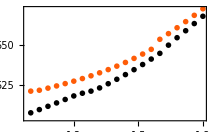
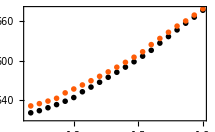

```mathematica
plots[[2,1]] = MapThread[ListPlot[Transpose[{nMatList,#}]&/@ #[[;;,;;,1]], Mesh->None,PlotMarkers->({#,Scaled[.04]}&/@#2),Evaluate[graphsOpts]]&,{{r12[[1]],r50[[1]]},markers}]
```

```mathematica
nNP=JohnsonChristyAuRefSize[#,radius]&;

radius = 12.5;
r12[[2]] =Table[nMat = nm &;
		 FindExtrema[#,wlength, 5., "Maxima"][[1]],
		{nm,nMatList}]&/@ {extFunc,scaFunc};
radius = 50.;
r50[[2]] =Table[nMat = nm &;
		 FindExtrema[#,wlength, 5., "Maxima"][[-1]],
		{nm,nMatList}]&/@ {extFunc,scaFunc};
```

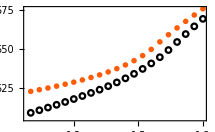
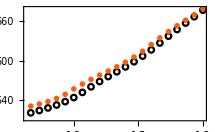

```mathematica
plots[[2,2]] = MapThread[ListPlot[Transpose[{nMatList,#}]&/@ #[[;;,;;,1]], Mesh->None,PlotMarkers->({#,Scaled[.04]}&/@Reverse@#2),Evaluate[graphsOpts]]&,{{r12[[2]],r50[[2]]},markers}]
```

#### Results

```mathematica
matex = MaTeX[#,ContentPadding->False,FontSize->fs]&;
flabels = Map[Style[#,texStyle]&,{{"a [nm]","λ_res [nm]"},{"nm [RIU]", "λ_res [nm]"}} ,{2}];
flabels = Map[matex,{{"a \\text{ [nm]}","\\lambda_{\\text{res}} \\text{ [nm]}"},{"n_\\text{m} \\text{ [RIU]}", "\\lambda_{\\text{res}}  \\text{ [nm]}"}} ,{2}];

PointLegend[{Directive[Gray],Directive[Gray]}, Style[#,texStyle]&/@{"No Size Correction","Size Correction"},Spacings-> 0.5,LegendMarkers->markers[[1,{1,-1}]],LegendMarkerSize->15, LegendLayout->"Row"];

LineLegend[{Directive[Black],Directive[Orange]}, Style[ #,texStyle]&/@{"Extintion","Scattering"},Spacings-> .5, LegendMarkerSize->15,LegendLayout->"Row"]

legend = Framed[Row[{%%,%}],RoundingRadius->10];
Export[FileNameJoin[{dir,"legend.svg"}],legend]
plotLabels = Map[Style[#,texStyle]&,{{"AuNP@Air","AuNP@Glass"},{"12.5 nm AuNP","50 nm AuNP"}},{2}];
```

5-Redshift/legend.svg

```mathematica
flabels ={#,#}&/@flabels;
plotLabels = Map[Style[#,texStyle]&,{{"AuNP@Air","AuNP@H_2O"},{"12.5 nm AuNP","50 nm AuNP"}},{2}];
```

```mathematica
plot = MapThread[Show[{#1,#2}, FrameLabel-> #3]&, Append[Transpose[plots],flabels],2];
plot = Row@Flatten@Map[Show[#1, AspectRatio-> 2, ImageSize-> 215/1.8]&,plot, {2}]
Export[FileNameJoin[{dir,"redShift2.pdf"}],plot]
```

-Graphics--Graphics--Graphics--Graphics-

5-Redshift/redShift2.pdf

```mathematica
plot = MapThread[Show[{#1,#2}, FrameLabel-> #3]&, Append[Transpose[plots],flabels],2];
plot = Row@Flatten@Map[Show[#1, AspectRatio-> 2, ImageSize-> 215/1.8]&,plot, {2}]
Export[FileNameJoin[{dir,"redShift2.pdf"}],plot]
```

-Graphics--Graphics--Graphics--Graphics-

5-Redshift/redShift2.pdf

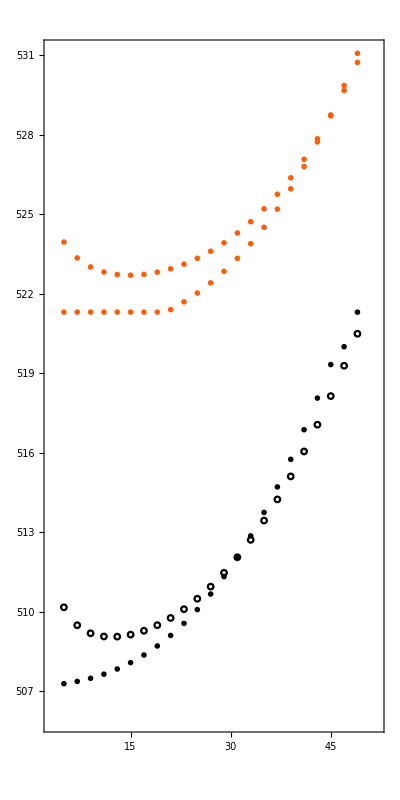
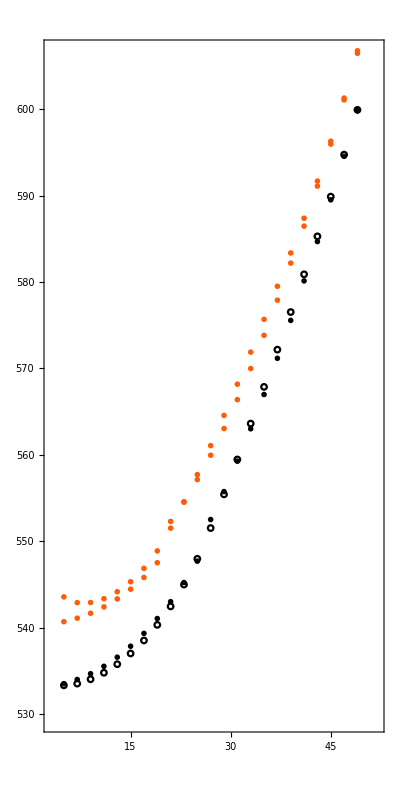
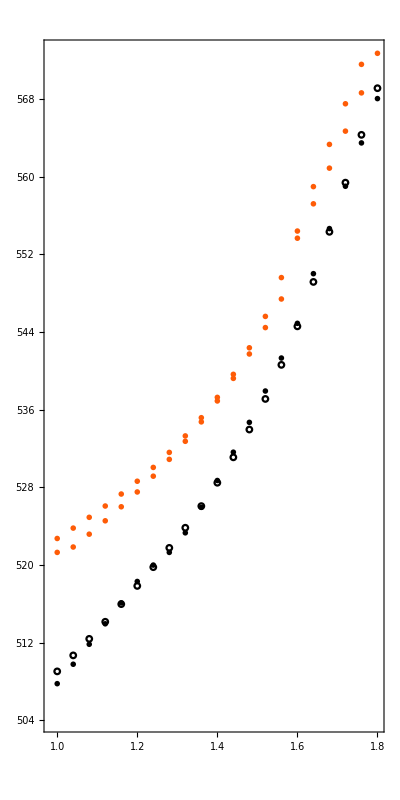
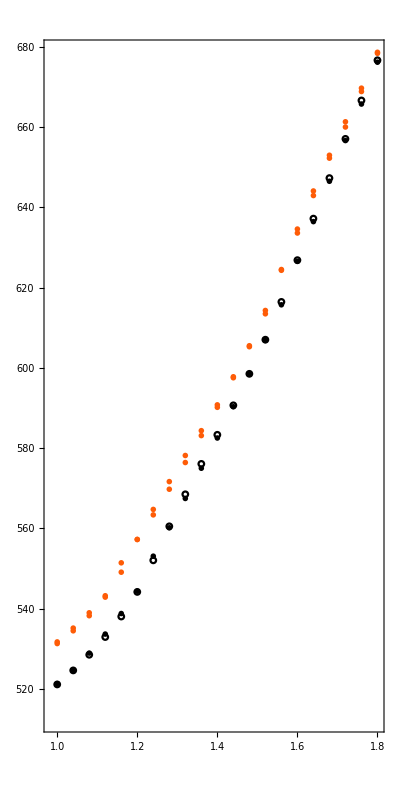

5-Redshift/redShift_PDF.pdf

```mathematica
plot = MapThread[Show[{#1,#2}]&, Transpose[plots],2];
plot = Row[Flatten[Map[Show[#1, AspectRatio-> 2, ImageSize-> 215/2]&, plot, {2}]]," "]
Export[FileNameJoin[{dir,"redShift_PDF.pdf"}],plot ]
```